```mathematica
(*Задание 1*)
(*а)метод Эйлера-Коши*)
f[x_,y_]=1+ 4y*Sin[x]-1.5 y^2;
h1 = 0.1;
h2 = 0.05;
a =0 ;
b = 1;
n1 = (b-a)/h1;
n2 = (b-a)/h2;
x0 = 0;
y0 = 0;
```

```mathematica
eulk1=Table[{x0,y0}={x0+h1,y0+h1/2*(f[x0,y0]+f[x0+h1,y0+h1*f[x0,y0]])},{i,0,n1-1}]
```

{{0.1,0.101247},{0.2,0.207482},{0.3,0.323702},{0.4,0.454796},{0.5,0.605201},{0.6,0.778257},{0.7,0.975239},{0.8,1.19429},{0.9,1.42973},{1.,1.6722}}

```mathematica
eulk1=Prepend[eulk1,{0,0}]
```

{{0,0},{0.1,0.101247},{0.2,0.207482},{0.3,0.323702},{0.4,0.454796},{0.5,0.605201},{0.6,0.778257},{0.7,0.975239},{0.8,1.19429},{0.9,1.42973},{1.,1.6722}}

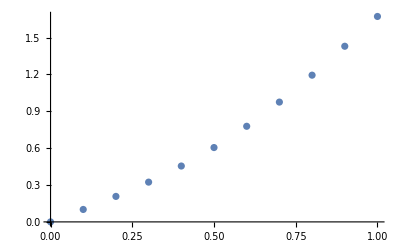

```mathematica
graphic1 = ListPlot[eulk1]
```

```mathematica
x0 = 0;
y0 = 0;
eulk2=Table[{x0,y0}={x0+h2,y0+h2/2*(f[x0,y0]+f[x0+h2,y0+h2*f[x0,y0]])},{i,0,n2-1}]
```

{{0.05,0.0501561},{0.1,0.100937},{0.15,0.152968},{0.2,0.206877},{0.25,0.263289},{0.3,0.322827},{0.35,0.386097},{0.4,0.453683},{0.45,0.526126},{0.5,0.603899},{0.55,0.687383},{0.6,0.776831},{0.65,0.872335},{0.7,0.97379},{0.75,1.08086},{0.8,1.19298},{0.85,1.30931},{0.9,1.4288},{0.95,1.55017},{1.,1.672}}

```mathematica
eulk2=Prepend[eulk2,{0,0}]
```

{{0,0},{0.05,0.0501561},{0.1,0.100937},{0.15,0.152968},{0.2,0.206877},{0.25,0.263289},{0.3,0.322827},{0.35,0.386097},{0.4,0.453683},{0.45,0.526126},{0.5,0.603899},{0.55,0.687383},{0.6,0.776831},{0.65,0.872335},{0.7,0.97379},{0.75,1.08086},{0.8,1.19298},{0.85,1.30931},{0.9,1.4288},{0.95,1.55017},{1.,1.672}}

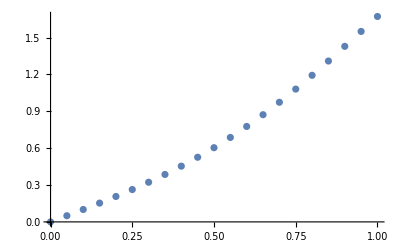

```mathematica
graphic2=ListPlot[eulk2]
```

```mathematica
(*б)метод Рунге-Кутта*)
Clear[x,y]
f[x_,y_]=1+ 4y*Sin[x]-1.5 y^2;
h1 = 0.1;
h2 = 0.05;
a =0 ;
b = 1;
n1 = (b-a)/h1;
n2 = (b-a)/h2;
x0 = 0;
y0 = 0;
```

```mathematica
sol1=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n1+1,k++,
k1[x_,y_]=h1*f[x,y];
k2[x_,y_]=h1*f[x+h1/2,y+k1[x,y]/2];
k3[x_,y_]=h1*f[x+h1/2,y+k2[x,y]/2];
k4[x_,y_]=h1*f[x+h1,y+k3[x,y]];
x=x+h1;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol1=Append[sol1,{x,y}]]
```

```mathematica
sol1
```

{{0,0},{0.1,0.100833},{0.2,0.206674},{0.3,0.322532},{0.4,0.453309},{0.5,0.603464},{0.6,0.776362},{0.7,0.973324},{0.8,1.19258},{0.9,1.42854},{1.,1.67198}}

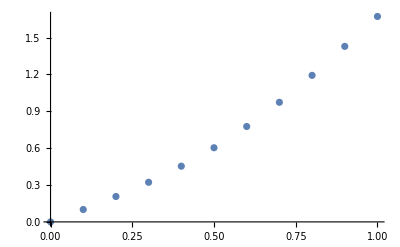

```mathematica
graphic3 = ListPlot[sol1]
```

```mathematica
sol2=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n2+1,k++,
k1[x_,y_]=h2*f[x,y];
k2[x_,y_]=h2*f[x+h2/2,y+k1[x,y]/2];
k3[x_,y_]=h2*f[x+h2/2,y+k2[x,y]/2];
k4[x_,y_]=h2*f[x+h2,y+k3[x,y]];
x=x+h2;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol2=Append[sol2,{x,y}]]
```

```mathematica
sol2
```

{{0,0},{0.05,0.0501042},{0.1,0.100834},{0.15,0.152815},{0.2,0.206674},{0.25,0.26304},{0.3,0.322533},{0.35,0.385761},{0.4,0.45331},{0.45,0.52572},{0.5,0.603466},{0.55,0.686929},{0.6,0.776365},{0.65,0.871866},{0.7,0.973329},{0.75,1.08043},{0.8,1.19258},{0.85,1.30897},{0.9,1.42854},{0.95,1.55002},{1.,1.67199}}

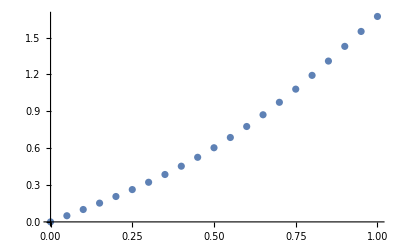

```mathematica
graphic4 = ListPlot[sol2]
```

```mathematica
(*с помощью функций DSolve и NDSolve*)
Clear[x,y]
eqn=y'[x]==1+ 4y[x]*Sin[x]-1.5(y[x])^2;
initialCondition=y[0]==0;
solutionDSolve=DSolve[{eqn,initialCondition},y,x];
y1[x_]=y[x]/. solutionDSolve
```

{((0.+1.70756×10^15 ⅈ) ⅇ^(ⅈ x) [ⅇ^(ⅈ x)]+(0.+0.666667 ⅈ) ⅇ^(ⅈ x) [ⅇ^(ⅈ x)])/([ⅇ^(ⅈ x)]+2.56134×10^15 [ⅇ^(ⅈ x)])}

```mathematica
Clear[x,y]
eqn=y'[x]==1+ 4y[x]*Sin[x]-1.5(y[x])^2;
initialCondition=y[0]==0;
solutionNDSolve=NDSolve[{eqn,initialCondition},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

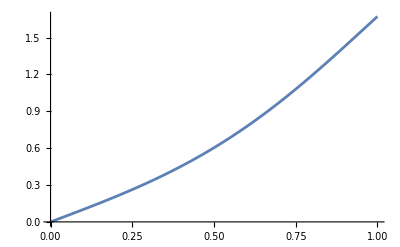

```mathematica
graphic5=Plot[Evaluate[y[x]/.solutionNDSolve],{x,0,1}]
```

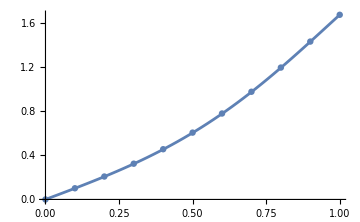

```mathematica
Show[graphic1,graphic5,ImageSize->Medium]
```

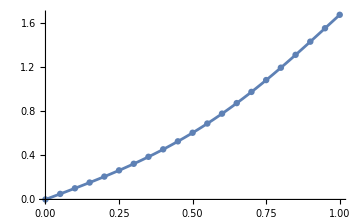

```mathematica
Show[graphic2,graphic5,ImageSize->Medium]
```

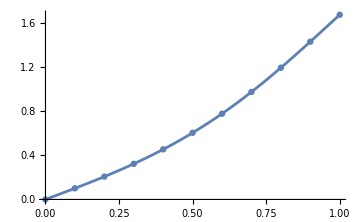

```mathematica
Show[graphic3,graphic5,ImageSize->Medium]
```

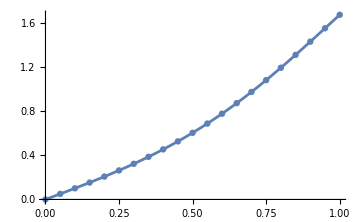

```mathematica
Show[graphic4,graphic5,ImageSize->Medium]
```

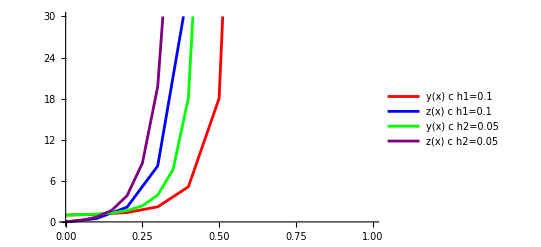

```mathematica
(*Задание 2*)
(*а)метод Эйлера*)
Clear[y, z,x]
a = 0;  b = 1;     
y0 = 1;        
z0 = 0;         
h1 = 0.1;       h2 = 0.05;
f[y_, z_] := y^2+3z;  
g[y_, z_] := 4f[y,z]+7z;      
n1 = Floor[(b - a)/h1]; 
 x = a; y = y0; z = z0; result1= {{x, y, z}};
    For[i = 1, i <= n1, i++,
      y = y + h1 * f[y, z]; 
      z = z + h1* g[y, z]; 
      x = x + h1;
      AppendTo[result1, {x, y, z}];  
    ];
n2 = Floor[(b - a)/h2];
 x = a; y = y0; z = z0; result2= {{x, y, z}};
    For[i = 1, i <= n2, i++,
      y = y + h2 * f[y, z]; 
      z = z + h2 * g[y, z]; 
      x = x + h2;
      AppendTo[result2, {x, y, z}];  
    ];
ListLinePlot[
 {
  result1[[All, {1, 2}]], result1[[All, {1, 3}]], 
  result2[[All, {1, 2}]], result2[[All, {1, 3}]]
 },
 PlotStyle -> {Red, Blue, Green, Purple},
 PlotLegends -> {"y(x) с h1=0.1", "z(x) с h1=0.1", 
   "y(x) с h2=0.05", "z(x) с h2=0.05"},

 PlotRange -> {{0,1},{0,30}}
]
```

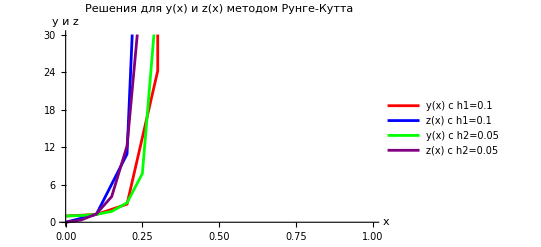

```mathematica
Clear[y,z,x]
a = 0;  b = 1;     
y0 = 1;        
z0 = 0;         
h1 = 0.1;       h2 = 0.05;
f[y_, z_] := y^2+3z;  
g[y_, z_] := 4f[y,z]+7z;   
n1=Floor[(b-a)/h1];
 x = a; y = y0; z = z0; result1= {{x, y, z}};
For[i=1,i<=n1,i++,
{k1y,k1z}={h1*f[y,z],h1*g[y,z]};
{k2y,k2z}={h1*f[y+0.5*k1y,z+0.5*k1z],h1*g[y+0.5*k1y,z+0.5*k1z]};
{k3y,k3z}={h1*f[y+0.5*k2y,z+0.5*k2z],h1*g[y+0.5*k2y,z+0.5*k2z]};
{k4y,k4z}={h1*f[y+k3y,z+k3z],h1*g[y+k3y,z+k3z]};
y=y+(1/6) (k1y+2*k2y+2*k3y+k4y);
z=z+(1/6) (k1z+2*k2z+2*k3z+k4z);
x=x+h1;
AppendTo[result1,{x,y,z}];  ];
n2=Floor[(b-a)/h2];
x = a; y = y0; z = z0; result2= {{x, y, z}};
For[i=1,i<=n1,i++,
{k1y,k1z}={h2*f[y,z],h2*g[y,z]};
{k2y,k2z}={h2*f[y+0.5*k1y,z+0.5*k1z],h2*g[y+0.5*k1y,z+0.5*k1z]};
{k3y,k3z}={h2*f[y+0.5*k2y,z+0.5*k2z],h2*g[y+0.5*k2y,z+0.5*k2z]};
{k4y,k4z}={h2*f[y+k3y,z+k3z],h2*g[y+k3y,z+k3z]};
y=y+(1/6) (k1y+2*k2y+2*k3y+k4y);
z=z+(1/6) (k1z+2*k2z+2*k3z+k4z);
x=x+h2;
AppendTo[result2,{x,y,z}];  ];
ListLinePlot[{result1[[All,{1,2}]],result1[[All,{1,3}]],result2[[All,{1,2}]],result2[[All,{1,3}]]},PlotStyle->{Red,Blue,Green,Purple},PlotLegends->{"y(x) с h1=0.1","z(x) с h1=0.1","y(x) с h2=0.05","z(x) с h2=0.05"},AxesLabel->{"x","y и z"},PlotLabel->"Решения для y(x) и z(x) методом Рунге-Кутта", PlotRange -> {{0,1},{0,30}}]
```

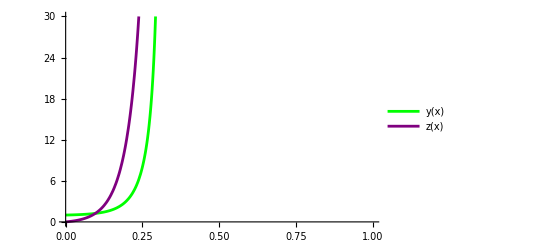

```mathematica
Clear[y,z,x]
eq1=y'[x]-(y[x])^2-3z[x]==0; 
eq2=z'[x]-4y'[x]-7z[x]==0; 
initialConditions={y[0]==1,z[0]==0};

numericalSolution=NDSolve[{eq1,eq2,initialConditions},{y,z},{x,0,1}];
Plot[Evaluate[{y[x],z[x]}/. numericalSolution],{x,0,1},PlotStyle->{Green,Purple},PlotLegends->{"y(x)","z(x)"},PlotRange->{{0,1},{0,30}}]
```